## wobbling motion even-even nuclei

### Determining the two parameters (w_1,w_2) which define the boson creation and annihilation operators used to diagonalize H_w

```mathematica
moi1=10;
moi2=25;
moi3=50;
A1=1/(2*moi1);
A2=1/(2*moi2);
A3=1/(2*moi3);
alpha[I_]:=I(A1+A2-2A3);
beta[I_]:=I(A2-A1);
w1[I_]:=Sqrt[1/2(alpha[I]/Sqrt[alpha[I]^2-beta[I]^2]+1)];
w2[I_]:=Sqrt[1/2(alpha[I]/Sqrt[alpha[I]^2-beta[I]^2]-1)];
```

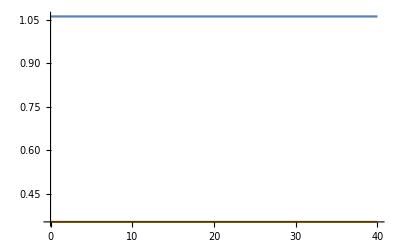

```mathematica
Plot[{w1[x],w2[x]},{x,0,40}]
```

```mathematica
wt1[t1_,t2_]:=If[t1!=t2,Sqrt[1/2(t1/Sqrt[t1^2-t2^2]+1)],-1];
wt2[t1_,t2_]:=If[t1!=t2,Sqrt[1/2(t1/Sqrt[t1^2-t2^2]-1)],-1];
```

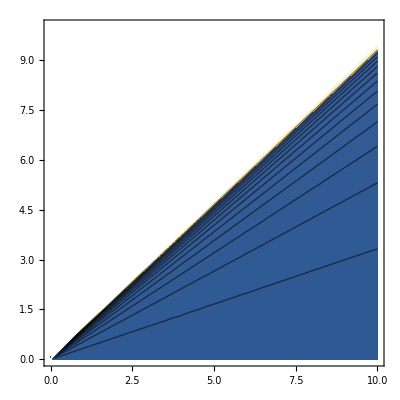

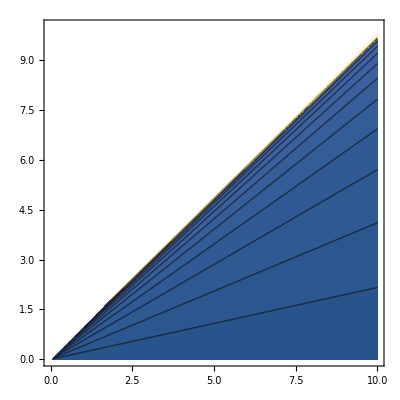

```mathematica
ContourPlot[{wt1[t1,t2]},{t1,0,10},{t2,0,10},Contours->20,ClippingStyle->None]
ContourPlot[{wt2[t1,t2]},{t1,0,10},{t2,0,10},Contours->20,ClippingStyle->None]
```